Уравнение задачи:

-a^2 u^(0,2)[x,t]+u^(1,0)[x,t]==0

t > 0, 0 < x < ∞

Начальные условия

u(x,0)= ϕ(x), x>0 
u(0,t) =  0,   t>0

ϕ(x)=Piecewise[{{(4h)/(3l)(x),, 0≤ x≤(3l)/4}, {(4h)/l(l-x),, (3l)/4< x≤ l}, {0,, x∉(0,l)}}]

Преобразование Фурье

U(λ,t) = 0.398942 ∫_(-∞)^∞ ⅇ^(-ⅈ x λ) u[x,t]ⅆx

a^2 λ^2 ux[λ,t]+ux^(0,1)[λ,t]==0

Фурье-образ начальной функции ϕ(x) имеет вид:

F[ϕ] = Φ[λ] = U(λ,0)= -(8-32 ⅇ^(-(9 ⅈ λ)/4)+24 ⅇ^(-3 ⅈ λ))/(9 √(2 π) λ^2)

Решение уравнения при помощи фурье-образов:

ux(λ,t) = ϕ[λ]ⅇ^(-SuperscriptBox[a, 2] SuperscriptBox[λ, 2] t) = {{ux→Function[{λ,t},(ⅇ^(-a^2 t λ^2) (-(8-32 ⅇ^(-(9 ⅈ λ)/4)+24 ⅇ^(-3 ⅈ λ))))/(9 √(2 π) λ^2)]}}

Решение в виде свёртки:

u(x,t) =∫_(-∞)^∞ ϕ(ξ)ⅇ^(-FractionBox[SuperscriptBox[(x - ξ), 2], 4 SuperscriptBox[a, 2] t])ⅆξ = -2.00601 a ⅇ^(-(9-4 x)^2/(64 a^2 t)) √t+1.50451 a ⅇ^(-(-3+x)^2/(4 a^2 t)) √t+0.501502 a ⅇ^(-x^2/(4 a^2 t)) √t+(-4.+1.33333 x) Erf[(-3+x)/(2 a √t)]+0.444444 x Erf[x/(2 a √t)]+4. Erf[(-9+4 x)/(8 a √t)]-1.77778 x Erf[(-9+4 x)/(8 a √t)]

Графики для моментов времени t_k=(k*l)/(4  a)

0.853609

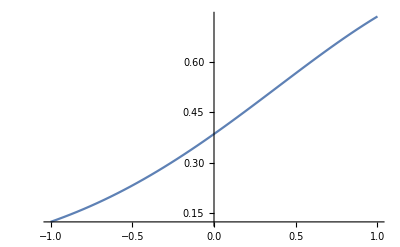

```mathematica
Clear["Global`*"];
Style[Text["Уравнение задачи:"],FontSize->18]
equation:=D[u[x,t],x]-a^2*D[u[x,t],{t,2}]==0
equation
Text["t > 0, 0 < x < ∞"]
h:=2;
l:=3;
f[x_]:=Which[0≤x≤3*l/4,4 * h * x/(3*l),
3*l/4<x≤l,4 * h*(l-x)/l,
l<x,0]
u[x_,0]:=f[x]/; x>0
u[0,t_]:=0/; t>0
Text["Начальные условия"]
Text["u(x,0)= ϕ(x), x>0 \nu(0,t) =  0,   t>0"]
Text["ϕ(x)=Piecewise[{{(4h)/(3l)(x),, 0≤ x≤(3l)/4}, {(4h)/l(l-x),, (3l)/4< x≤ l}, {0,, x∉(0,l)}}]"]
Style[Text["Преобразование Фурье"],FontSize->18]
ux[λ_,t_]:=1/(2*Pi)^0.5*Integrate[u[x,t]*E^(-ⅈ*λ*x),{x,-∞,∞}]
ux[λ_,0]:=FourierTransform[f[x],x,λ,FourierParameters->{0, -1}]
Print[Text["U(λ,t) = "],ux[λ,t]]
Clear[ux]
newEquation:=D[ux[λ,t],t]+a^2*λ^2*ux[λ,t]==0/.ux[λ,t]->ux[λ,t]
newEquation
Style[Text["Фурье-образ начальной функции ϕ(x) имеет вид: "],FontSize->18]
ux[λ_,0]:=FourierTransform[f[x],x,λ,FourierParameters->{0, -1}]
Print[Text["F[ϕ] = Φ[λ] = U(λ,0)= "],ux[λ,0]]
Style[Text["Решение уравнения при помощи фурье-образов:"],FontSize->18]
ux[λ_,0]:=FourierTransform[f[x],x,λ,FourierParameters->{0, -1}]
equationSolve=DSolve[newEquation,ux,{λ,t}];
Print[Text["ux(λ,t) = ϕ[λ]ⅇ^(-SuperscriptBox[a, 2] SuperscriptBox[λ, 2] t) = "],equationSolve/.C[1][λ]->ux[λ,0]]
Style[Text["Решение в виде свёртки: "],FontSize->18]
u[x_,t_]:= 1/(2*a*(Pi*t)^0.5)*Integrate[f[ξ]*ⅇ^(-(x-ξ)^2/(4*a^2*t)),{ξ,-∞,∞}]
Print [Text["u(x,t) =∫_(-∞)^∞ ϕ(ξ)ⅇ^(-FractionBox[SuperscriptBox[(x - ξ), 2], 4 SuperscriptBox[a, 2] t])ⅆξ = "],u[x,t]//Simplify]
Style[Text["Графики для моментов времени t_k=(k*l)/(4  a)"],FontSize->18]
t[k_]:=k*l/(4*a)/.a->1
u[2,t[1]]/.a->1
Plot[u[x,t[1]]/.a->1,{x,-1,1}]
```